## 5.2 Predicting sequences

This section deals with the prediction of the next value in a sequence. For instance, this is plays an important role in language modeling (e.g. predicting the next word in a text). Here, we cover some basic concepts. In the course on statistics and time series you will see more on prediction of time series.

In Wolfram Language, sequence prediction can be done with the function SequencePredict. The usage of this function will be illustrated with several simple examples. The examples will be used to give a brief introduction to the theory behind sequence prediction.

### Simple example 1 - One sequence

Suppose that we observed the following sequence of sunny (“S”) and cloudy (“C”) days:

```mathematica
spSC=SequencePredict[{{"C","S","S","S","C","C","S","S","S","S","S"}}]
```

SequencePredictorFunction[…]

```mathematica
spSC[[1]]
```

<|Preprocessor→ToMLDataset,Processor→IntegerEncodeNominalSequence,PerformanceGoal→Automatic,Model→<|Method→Markov,Order→1,Smoothing→KneserNey,Processor→FirstValues,TokenNumber→2,VocabularySize→4,TokenizationMapping→<|0→1,-∞→2,∞→3,2→4,1→5|>,UnknownToken→1,StartToken→2,StopToken→3,LogProbabilities→<|1Gram→{-0.90309,0.,-0.681241,-0.425969,-0.535113},2Gram→SparseArray[…]|>,Discounts→<|1Gram→<|D1→0.5,D2→1,D3+→1.5|>,2Gram→<|D1→0.5,D2→1,D3+→1.5|>|>,LogBackoffWeights→<|1Gram→{-0.30103,0.,-0.30103,0.,-0.50515}|>,Indexes→<|1Gram→MachineLearning`SortedHashAssociation[…]|>,RestLogProbabilities→<|1Gram→{-1.13717,0.,-0.940879,-0.703518,-0.211419}|>|>|>

According to this predictor, what is the most likely after a sunny day?

```mathematica
spSC[{"S"}]
```

S

and after a cloudy day?

```mathematica
spSC[{"C"}]
```

S

Predictions are probabilistic:

Probabilities of sunny or cloudy day after a sunny day:

```mathematica
afterS=spSC[{"S"},"Probabilities"]
```

<|S→0.784375,C→0.215625|>

Probabilities of sunny or cloudy day after a cloudy day:

```mathematica
afterC=spSC[{"C"},"Probabilities"]
```

<|S→0.575,C→0.425|>

```mathematica
transmat={Values[afterS],Values[afterC]}
```

{{0.784375,0.215625},{0.575,0.425}}

The transition probabilities between states can be summarised in a transition matrix as follows:

```mathematica
Grid[Prepend[MapThread[Prepend,{{Values[afterS],Values[afterC]},Keys[afterS]}],Prepend[Keys[afterC],""]]]
```

| S | C
S | 0.784375 | 0.215625
C | 0.575 | 0.425

Transitions and their probabilities can also be visualised as a graph:

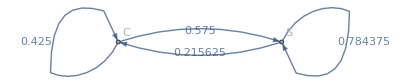

```mathematica
Graph[{Labeled["S"->"S",transmat[[1,1]]],Labeled["C"->"C",transmat[[2,2]]],Labeled["S"->"C",transmat[[1,2]]],Labeled["C"->"S",transmat[[2,1]]]},VertexLabels->"Name"]
```

### The Markov method

Note that the method used by SequencePredict is the Markov method. In plain terms, the model used here assumes that the probability of an element in the sequence only depends on the previous element in the sequence. 

I will not cover the details of the method in detail here.

If you are familiar with conditional probability: Given a sequence of observations {X_1,X_2,....,X_T}, the model assumes that the probability of the sequence can be expressed as

P({X_1,X_2,....,X_T})=P(X_1)P(X_2|X_1)P(X_3|X_2)...P(X_T|X_(T-1)),

where P(X_t|X_(t-1)) is the probability of observing the value X_t at step t in the sequence given that the value X_(t-1) was observed in the previous step.

The transition matrix contains the quantities

A_ij=P(X_(t+1)=j|X_t=i) .

In our simple example, X_t can be C or S. The i and j in the transition matrix can then take values in the set {C,S}.

Examples:
A_SS=P(X_(t+1)="S"|X_t="S")
A_SC=P(X_(t+1)="C"|X_t="S")

If interested in more technical details that are beyond the scope of this course, see Chapter 17 of Kevin P. Murphy “Machine Learning: A Probabilistic Perspective” The MIT Press (2012).

Mathematica uses the Kneser-Ney smoothing method to calculate the elements of the transition matrix. This is a popular method for language modelling. Details on this are much beyond the scope of this course. If interested see, e.g., the following paper: Stanley F. Chen, Joshua Goodman, “An empirical study of smoothing techniques for language modeling”, Computer Speech & Language, 13, 359-394 (1999). http://www.sciencedirect.com/science/article/pii/S0885230899901286

#### Task for you - Estimating the transition matrix by counting

Task 1. For the example presented above, one could estimate the elements of the transition matrix by just counting. For instance,

A_CC=P(X_(t+1)="C"|X_t="C")=(Number of times we observe the subsequence C-C)/(Number of times we observe C-*) ,

where “*” stands for both C and S. 

Calculate all the elements in the matrix. Do you obtain exactly the same as Mathematica?

### Simple example 2 - Using several sequences

Let us consider data consisting of three colours:

```mathematica
RGBColor["Red"]
RGBColor["Blue"]
RGBColor[0,0.79,0.09]
```

RGBColor[1., 0., 0.]

RGBColor[0., 0., 1.]

RGBColor[0, 0.79, 0.09]

In the previous example, we used a single sequence but SequencePredict can be trained with several sequences. Let us train a sequence predictor using several sequences:

```mathematica
sp=SequencePredict[{{RGBColor[1., 0., 0.],RGBColor[0., 0., 1.]},{RGBColor[0, 0.79, 0.09],RGBColor[0., 0., 1.],RGBColor[0, 0.79, 0.09]},{RGBColor[0., 0., 1.],RGBColor[0, 0.79, 0.09],RGBColor[1., 0., 0.]},{RGBColor[0., 0., 1.],RGBColor[0, 0.79, 0.09]},{RGBColor[1., 0., 0.],RGBColor[0., 0., 1.],RGBColor[0, 0.79, 0.09]}}]
```

SequencePredictorFunction[…]

What are the possible operations we can do with the trained predictor?

```mathematica
sp[{RGBColor[1., 0., 0.]},"Properties"]
```

{NextElement,NextSequence,RandomNextElement,Probabilities,SequenceLogProbability,SequenceProbability}

As before, we can calculate probabilities for the next colour after a certain colour:

```mathematica
sp[{RGBColor[0., 0., 1.]},"Probabilities"]
```

<|RGBColor[0, 0.79, 0.09]→0.810304,RGBColor[0., 0., 1.]→0.105386,RGBColor[1., 0., 0.]→0.0843091|>

```mathematica
sp[{RGBColor[0, 0.79, 0.09]},"Probabilities"]
```

<|RGBColor[0, 0.79, 0.09]→0.170686,RGBColor[0., 0., 1.]→0.435993,RGBColor[1., 0., 0.]→0.393321|>

```mathematica
sp[{RGBColor[1., 0., 0.]},"Probabilities"]
```

<|RGBColor[0, 0.79, 0.09]→0.227979,RGBColor[0., 0., 1.]→0.544041,RGBColor[1., 0., 0.]→0.227979|>

What is the probability of a sequence?

```mathematica
sp[{RGBColor[0, 0.79, 0.09],RGBColor[0., 0., 1.],RGBColor[1., 0., 0.]},"SequenceProbability"]
```

0.0114842

The predictor also gives the logarithm of the probability which is useful when the probability of a sequence is very small.

```mathematica
sp[{RGBColor[0, 0.79, 0.09],RGBColor[0., 0., 1.],RGBColor[1., 0., 0.]},"SequenceLogProbability"]
```

-4.46678

Indeed, this is the logarithm of the sequence

```mathematica
Log[sp[{RGBColor[0, 0.79, 0.09],RGBColor[0., 0., 1.],RGBColor[1., 0., 0.]},"SequenceProbability"]]
```

-4.46678

What is the probability of each next element? It only depends on the last colour.

```mathematica
sp[{RGBColor[1., 0., 0.],RGBColor[0., 0., 1.]},"Probabilities"]
```

<|RGBColor[0, 0.79, 0.09]→0.810304,RGBColor[0., 0., 1.]→0.105386,RGBColor[1., 0., 0.]→0.0843091|>

Draw the next element randomly:

```mathematica
sp[{RGBColor[1., 0., 0.],RGBColor[0., 0., 1.]},"RandomNextElement"->20]
```

{RGBColor[0, 0.79, 0.09],RGBColor[0., 0., 1.],RGBColor[1., 0., 0.],RGBColor[0, 0.79, 0.09],RGBColor[0., 0., 1.],RGBColor[0, 0.79, 0.09],RGBColor[0., 0., 1.],RGBColor[0, 0.79, 0.09],RGBColor[1., 0., 0.],RGBColor[0., 0., 1.],RGBColor[0, 0.79, 0.09],RGBColor[1., 0., 0.],RGBColor[0, 0.79, 0.09],RGBColor[0, 0.79, 0.09],RGBColor[0, 0.79, 0.09],RGBColor[0., 0., 1.],RGBColor[0, 0.79, 0.09],RGBColor[0., 0., 1.],RGBColor[0, 0.79, 0.09],RGBColor[1., 0., 0.]}

Green is the most probable and will typically appear more often, followed by blue and red

```mathematica
Tally[%]
```

{{RGBColor[0, 0.79, 0.09],10},{RGBColor[0., 0., 1.],6},{RGBColor[1., 0., 0.],4}}

Predict the most likely next element and reuse this intermediate guess to predict the following element:

```mathematica
sp[{RGBColor[0., 0., 1.],RGBColor[0, 0.79, 0.09]},"NextElement"->4]
```

{RGBColor[0., 0., 1.],RGBColor[0, 0.79, 0.09],RGBColor[0., 0., 1.],RGBColor[0, 0.79, 0.09]}

```mathematica
sp[{RGBColor[0, 0.79, 0.09]},"NextElement"->4]
```

{RGBColor[0., 0., 1.],RGBColor[0, 0.79, 0.09],RGBColor[0., 0., 1.],RGBColor[0, 0.79, 0.09]}

```mathematica
sp[{RGBColor[0., 0., 1.],RGBColor[1., 0., 0.]},"NextElement"->4]
```

{RGBColor[0., 0., 1.],RGBColor[0, 0.79, 0.09],RGBColor[0., 0., 1.],RGBColor[0, 0.79, 0.09]}

```mathematica
sp[{RGBColor[1., 0., 0.],RGBColor[0., 0., 1.]},"NextElement"->4]
```

{RGBColor[0, 0.79, 0.09],RGBColor[0., 0., 1.],RGBColor[0, 0.79, 0.09],RGBColor[0., 0., 1.]}

```mathematica
sp[{RGBColor[1., 0., 0.],RGBColor[0, 0.79, 0.09]},"NextElement"->8]
```

{RGBColor[0., 0., 1.],RGBColor[0, 0.79, 0.09],RGBColor[0., 0., 1.],RGBColor[0, 0.79, 0.09],RGBColor[0., 0., 1.],RGBColor[0, 0.79, 0.09],RGBColor[0., 0., 1.],RGBColor[0, 0.79, 0.09]}

Predict the most likely following sequence:

```mathematica
sp[{RGBColor[0, 0.79, 0.09],RGBColor[0., 0., 1.],RGBColor[0, 0.79, 0.09]},"NextSequence"->3]
```

{RGBColor[1., 0., 0.],RGBColor[0., 0., 1.],RGBColor[0, 0.79, 0.09]}

```mathematica
sp[{RGBColor[0., 0., 1.],RGBColor[0, 0.79, 0.09],RGBColor[1., 0., 0.]},"NextElement"->3]
```

{RGBColor[0., 0., 1.],RGBColor[0, 0.79, 0.09],RGBColor[0., 0., 1.]}

#### Task for you

Task 2: The sequence {RGBColor[0., 0., 1.],RGBColor[0, 0.79, 0.09],RGBColor[0., 0., 1.],RGBColor[0, 0.79, 0.09]} seems to be the only one that is stable after all, why?

### Higher order predictor

The predictor used above corresponds to a Markov process of order 1. This means that the next outcome in a sequence only depends on the current outcome. This might be unrealistic in some situations since an outcome might have longer memory, i.e. it might depend on n previous outcomes for n>1. For a given set of training sequences, trainseq, one can use the SequencePredict function to train Markov process with memory n as follows:

SequencePredict[trainseq,Method→{“Markov”,”Order”→ n}]

Let us train an order 2 predictor for the colour sequence used above:

```mathematica
sp2=SequencePredict[{{RGBColor[1., 0., 0.],RGBColor[0., 0., 1.]},{RGBColor[0, 0.79, 0.09],RGBColor[0., 0., 1.],RGBColor[0, 0.79, 0.09]},{RGBColor[0., 0., 1.],RGBColor[0, 0.79, 0.09],RGBColor[1., 0., 0.]},{RGBColor[0., 0., 1.],RGBColor[0, 0.79, 0.09]},{RGBColor[1., 0., 0.],RGBColor[0., 0., 1.],RGBColor[0, 0.79, 0.09]}},Method->{"Markov","Order"-> 2}]
```

SequencePredictorFunction[…]

For the memory 2 predictor, the probabilities of any colour after a pair of colours,

```mathematica
sp2[{RGBColor[1., 0., 0.],RGBColor[0., 0., 1.]},"Probabilities"]
```

<|RGBColor[0, 0.79, 0.09]→0.782258,RGBColor[0., 0., 1.]→0.120968,RGBColor[1., 0., 0.]→0.0967742|>

are not identical to the probabilities after a single colour:

```mathematica
sp2[{RGBColor[0., 0., 1.]},"Probabilities"]
```

<|RGBColor[0, 0.79, 0.09]→0.736562,RGBColor[0., 0., 1.]→0.146354,RGBColor[1., 0., 0.]→0.117084|>

```mathematica
sp2[{RGBColor[0., 0., 1.],RGBColor[0, 0.79, 0.09]},"Probabilities"]
```

<|RGBColor[0, 0.79, 0.09]→0.129964,RGBColor[0., 0., 1.]→0.379061,RGBColor[1., 0., 0.]→0.490975|>

In contrast, for the memory 1 predictor, the probabilities only depend on the last colour:

```mathematica
sp[{RGBColor[1., 0., 0.],RGBColor[0., 0., 1.]},"Probabilities"]
```

<|RGBColor[0, 0.79, 0.09]→0.810304,RGBColor[0., 0., 1.]→0.105386,RGBColor[1., 0., 0.]→0.0843091|>

```mathematica
sp[{RGBColor[0., 0., 1.]},"Probabilities"]
```

<|RGBColor[0, 0.79, 0.09]→0.810304,RGBColor[0., 0., 1.]→0.105386,RGBColor[1., 0., 0.]→0.0843091|>

The sequences in the memory 2 case differ from those in the memory 1 case and are perhaps in better agreement with our human intuition:

```mathematica
sp2[{RGBColor[1., 0., 0.],RGBColor[0., 0., 1.]},"NextElement"->8]
```

{RGBColor[0, 0.79, 0.09],RGBColor[1., 0., 0.],RGBColor[0., 0., 1.],RGBColor[0, 0.79, 0.09],RGBColor[1., 0., 0.],RGBColor[0., 0., 1.],RGBColor[0, 0.79, 0.09],RGBColor[1., 0., 0.]}

Compare with the memory 1 case:

```mathematica
sp[{RGBColor[1., 0., 0.],RGBColor[0., 0., 1.]},"NextElement"->8]
```

{RGBColor[0, 0.79, 0.09],RGBColor[0., 0., 1.],RGBColor[0, 0.79, 0.09],RGBColor[0., 0., 1.],RGBColor[0, 0.79, 0.09],RGBColor[0., 0., 1.],RGBColor[0, 0.79, 0.09],RGBColor[0., 0., 1.]}

### Application: Predicting text - The Raven

Language modelling is an important application of machine learning sequence prediction. SequencePredict can be used to make a statistical language model which are probability distributions over sequences of words.

In particular, here we look at an application for sentence completion using the text from The Raven by Edgar Allan Poe.

Let us first build a word cloud to get an idea of the words appearing in the test:

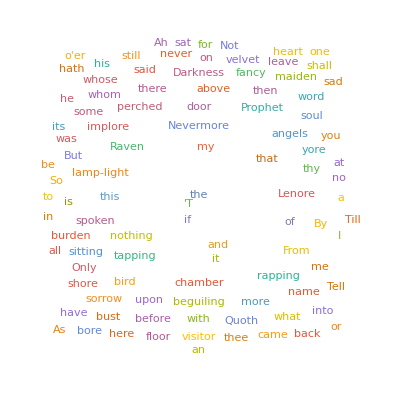

```mathematica
WordCloud[TextWords[ExampleData[{"Text","TheRaven"}]]]
```

Let us use the text to train a sequence predictor:

```mathematica
spRaven=SequencePredict[{TextWords[ExampleData[{"Text","TheRaven"}]]}]
```

SequencePredictorFunction[…]

Use the train predictor to predict the next word in “the raven is”

```mathematica
spRaven[{"the","raven","is"}]
```

the

```mathematica
spRaven[{"is"}]
```

the

The result makes sense and is the one with the highest probability according to the predictor. One can look at other options with lower probability which, in this particular example, seem to make less sense than “the”:

```mathematica
Take[Reverse[Sort[spRaven[{"is"},"Probabilities"]]],10]
```

<|the→0.0509391,I→0.0289398,and→0.0261899,my→0.0216067,of→0.0188568,that→0.013357,a→0.0124403,door→0.0124403,this→0.0115237,is→0.0115237|>

Training a predictor with longer memory might give more sensible results.